## Linear-time Kernel Stein Discrepancy

Evalute the population kernel Stein discrepancy where p(x) = N(0, 1), and q(x)=N(mu_q, sigma_q^2).
Assume that a Gaussian kernel is used.

```mathematica
eyt1=Expectation[x^2  Exp[-(x-y)^2/(2*Subscript[s, k])],y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(ⅇ^(-(x-μ_q)^2/(2 (s_k+σ_q^2))) x^2)/(√(1/s_k+1/σ_q^2) σ_q)

```mathematica
Subscript[s, k]=Subscript[σ, k]^2
```

σ_k^2

```mathematica
η=1/Subscript[s, k]^2+1/Subscript[s, k]
```

1/σ_k^4+1/σ_k^2

```mathematica
a1=-η*Expectation[eyt1,x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

((-1/σ_k^4-1/σ_k^2) (μ_q^2 σ_k^2+(2 μ_q^2+σ_k^2) σ_q^2+σ_q^4))/((σ_k^2+2 σ_q^2) √(1+(2 σ_q^2)/σ_k^2))

```mathematica
Simplify[a1]
```

-((1+σ_k^2) (σ_q^2 (σ_k^2+σ_q^2)+μ_q^2 (σ_k^2+2 σ_q^2)))/(σ_k^4 (σ_k^2+2 σ_q^2) √(1+(2 σ_q^2)/σ_k^2))

```mathematica
ext2=-η*Expectation[y^2  Exp[-(x-y)^2/(2*Subscript[s, k])],x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(ⅇ^(-(y-μ_q)^2/(2 (σ_k^2+σ_q^2))) y^2 (-1/σ_k^4-1/σ_k^2))/(√(1/σ_k^2+1/σ_q^2) σ_q)

```mathematica
a2=Expectation[ext2,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

-((1+σ_k^2) (μ_q^2 σ_k^2+(2 μ_q^2+σ_k^2) σ_q^2+σ_q^4))/(σ_k^4 (σ_k^2+2 σ_q^2) √(1+(2 σ_q^2)/σ_k^2))

```mathematica
ext3=(2*η+1)*Expectation[x y Exp[-(x-y)^2/(2*Subscript[s, k])], x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(ⅇ^(-(y-μ_q)^2/(2 (σ_k^2+σ_q^2))) y (1+2 (1/σ_k^4+1/σ_k^2)) σ_k^2 √(1/σ_k^2+1/σ_q^2) σ_q (μ_q σ_k^2+y σ_q^2))/((σ_k^2+σ_q^2)^2)

```mathematica
a3=Expectation[ext3,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

((2+2 σ_k^2+σ_k^4) √(1+(2 σ_q^2)/σ_k^2) (σ_q^4+μ_q^2 (σ_k^2+2 σ_q^2)))/((σ_k^3+2 σ_k σ_q^2)^2)

```mathematica
ext4=(1/Subscript[s, k])*Expectation[Exp[-(x-y)^2/(2*Subscript[s, k])], x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(ⅇ^(-(y-μ_q)^2/(2 (σ_k^2+σ_q^2))))/(σ_k^2 √(1/σ_k^2+1/σ_q^2) σ_q)

```mathematica
a4=Expectation[ext4,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

1/(σ_k^2 √(1+(2 σ_q^2)/σ_k^2))

```mathematica
kstein=Simplify[a1+a2+a3+a4]
```

((-1+σ_q^2)^2+μ_q^2 (σ_k^2+2 σ_q^2))/((σ_k^2+2 σ_q^2) √(1+(2 σ_q^2)/σ_k^2))

```mathematica
kstein/.Subscript[σ, q]-> 1
```

μ_q^2/(√(1+2/σ_k^2))

```mathematica
kstein/. Subscript[μ, q]-> 0
```

((-1+σ_q^2)^2)/((σ_k^2+2 σ_q^2) √(1+(2 σ_q^2)/σ_k^2))

## Variance under H_1

U-statistic kernel  h_p

```mathematica
logp[x_]:=-x^2/2
ker[x_,y_,s_]:=Exp[-(x-y)^2/(2*s)]
Dkx[x_,y_,s_]:=D[ker[x,y,s],x]
Dky[x_,y_,s_]:=D[ker[x,y,s],y]
Dkxy[x_,y_,s_]:=D[Dkx[x,y,s],y]
```

```mathematica
h[x_,y_]:=logp'[x] ker[x,y,Subscript[s, k]] logp'[y]+logp'[y] Dkx[x,y,Subscript[s, k]]+ logp'[x] Dky[x,y,Subscript[s, k]]+Dkxy[x,y,Subscript[s, k]]
```

```mathematica
Simplify[h[x,y]]
```

(ⅇ^(-(x-y)^2/(2 σ_k^2)) (-(x-y)^2-(-1+x^2-2 x y+y^2) σ_k^2+x y σ_k^4))/σ_k^4

```mathematica
exh = Expectation[h[x,y],x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(ⅇ^(-(y-μ_q)^2/(2 (σ_k^2+σ_q^2))) (-μ_q^2 (1+σ_k^2)+(-1+σ_q^2) (y^2+(-1+y^2) σ_k^2+(-1+y^2) σ_q^2)+y μ_q (2+σ_k^4+σ_k^2 (2+σ_q^2))))/(√(1/σ_k^2+1/σ_q^2) σ_q (σ_k^2+σ_q^2)^2)

```mathematica
eh=Expectation[exh,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(1+μ_q^2 σ_k^2+2 (-1+μ_q^2) σ_q^2+σ_q^4)/((σ_k^2+2 σ_q^2) √(1+(2 σ_q^2)/σ_k^2))

```mathematica
Simplify[kstein-eh]
```

0

```mathematica
Factor[h[x,y]^2]
```

(ⅇ^(-(x-y)^2/σ_k^2) (x^2-2 x y+y^2-σ_k^2+x^2 σ_k^2-2 x y σ_k^2+y^2 σ_k^2-x y σ_k^4)^2)/σ_k^8

```mathematica
Simplify[h[x,y]^2]
```

(ⅇ^(-(x-y)^2/σ_k^2) ((x-y)^2+(-1+x^2-2 x y+y^2) σ_k^2-x y σ_k^4)^2)/σ_k^8

Variance under H_1_□

```mathematica
Subscript[σ, q]=1
Subscript[σ, k]=1
```

1

1

```mathematica
exh2 = Expectation[h[x,y]^2,x\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]
```

(ⅇ^(-1/3 (y-μ_q)^2) (81+171 y^2+16 y^4+(7 y-2 μ_q) μ_q (-18+8 y^2+7 y μ_q-2 μ_q^2)))/(81 √3)

```mathematica
Collect[exh2 ,y]
```

(16 ⅇ^(-1/3 (y-μ_q)^2) y^4)/(81 √3)+(56 ⅇ^(-1/3 (y-μ_q)^2) y^3 μ_q)/(81 √3)+(ⅇ^(-1/3 (y-μ_q)^2) y^2 (171+33 μ_q^2))/(81 √3)+(ⅇ^(-1/3 (y-μ_q)^2) y (-126 μ_q-28 μ_q^3))/(81 √3)+(ⅇ^(-1/3 (y-μ_q)^2) (81+36 μ_q^2+4 μ_q^4))/(81 √3)

```mathematica
eh2 = Assuming[Subscript[σ, q]>0&&Subscript[μ, q]∈Reals,Expectation[exh2,y\[Distributed]NormalDistribution[Subscript[μ, q],Subscript[σ, q]]]]
```

(62+80 μ_q^2+25 μ_q^4)/(25 √5)

```mathematica
eh
```

(2+μ_q^2+2 (-1+μ_q^2))/(3 √3)

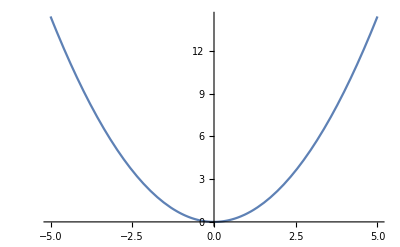

```mathematica
Plot[eh,{Subscript[μ, q],-5,5}]
```

```mathematica
e2h = eh^2
```

1/27 (2+μ_q^2+2 (-1+μ_q^2))^2

```mathematica
varh = Simplify[eh2-e2h]
```

62/(25 √5)+(16 μ_q^2)/(5 √5)+(-1/3+1/(√5)) μ_q^4

```mathematica
slope=Simplify[e2h/(2*varh)]
```

(125 μ_q^4)/(372 √5+480 √5 μ_q^2+50 (-5+3 √5) μ_q^4)